# Lab #7

## Craig Fox

Clear initial definitions

```mathematica
Remove["Global`*"]
```

Part 1

```mathematica
f = (x^2+y^2)/2
```

1/2 (x^2+y^2)

```mathematica
v = Grad[f,{x,y}]
```

{x,y}

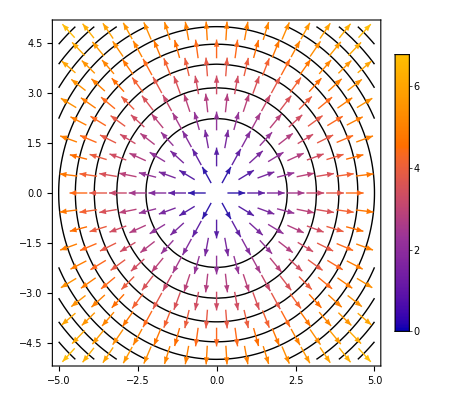

```mathematica
Show[ContourPlot[f,{x,-5,5},{y,-5,5},ContourShading->None],VectorPlot[v,{x,-5,5},{y,-5,5},PlotLegends->Automatic]]
```

```mathematica
Div[v,{x,y}]
```

2

This is what I expected.

```mathematica
Curl[Flatten[{v,0}],{x,y,z}]
```

{0,0,0}

This is expected because the curl of any gradient is always 0

Part 2

```mathematica
f = -1/Sqrt[x^2+y^2+z^2]
```

-1/(√(x^2+y^2+z^2))

```mathematica
v= Grad[f,{x,y,z}]
```

{x/((x^2+y^2+z^2)^(3/2)),y/((x^2+y^2+z^2)^(3/2)),z/((x^2+y^2+z^2)^(3/2))}

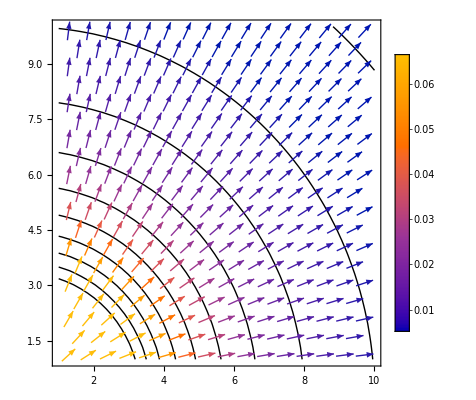

```mathematica
feq=f/.{z->0};
veq = (v/.{z->0})[[1;;2]];
Show[ContourPlot[feq,{x,1,10},{y,1,10},ContourShading->None],VectorPlot[veq,{x,1,10},{y,1,10},PlotLegends->Automatic]]
```

```mathematica
Simplify[Div[v,{x,y,z}]]
```

0

The Laplacian is zero because	 the gradient does not have any divergence as seen on the vector plot in how all the lines are copying each other in radiating from 0,0.

```mathematica
Simplify[ToPolarCoordinates[veq]]
```

{√(1/((x^2+y^2)^2)),ArcTan[x/((x^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2))]}

Point Charges are the physical situation that these model. Coulomb’s law matches this equation.

Part 3

```mathematica
v={-y/(x^2+y^2),x/(x^2+y^2)}
```

{-y/(x^2+y^2),x/(x^2+y^2)}

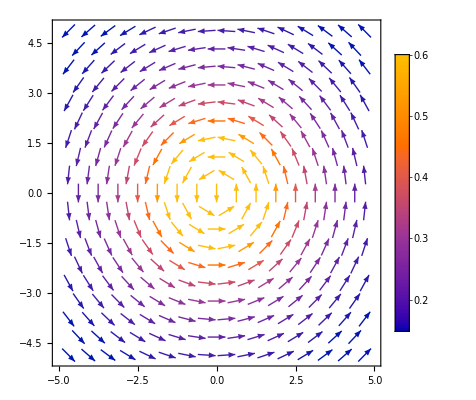

```mathematica
VectorPlot[v,{x,-5,5},{y,-5,5},PlotLegends->Automatic]
```

```mathematica
Simplify[Curl[v,{x,y}]]
```

0

The curl is 0 because as you can see from the vector plot, the vectors point in a concentric circles around the central point, so the curl is never changing.

```mathematica
Simplify[ToPolarCoordinates[v]]
```

{√(1/(x^2+y^2)),ArcTan[-y/(x^2+y^2),x/(x^2+y^2)]}

This equation models a magnetic field around a wire with a current running through it.